System 2 : ok

```mathematica
DSolve[{nd''[z]+c*nd'[z]+((1-s)*(r+1)-1)*nd[z]==0,no''[z]+c*no'[z]-no[z]==0},{nd,no},z]
```

{{nd→Function[{z},ⅇ^(1/2 (-c-√(c^2-4 r+4 s+4 r s)) z) C[1]+ⅇ^(1/2 (-c+√(c^2-4 r+4 s+4 r s)) z) C[2]],no→Function[{z},ⅇ^(1/2 (-c-√(4+c^2)) z) C[3]+ⅇ^(1/2 (-c+√(4+c^2)) z) C[4]]}}

System 7 : too complex... (understandable, I made a choice concerning the values in exp and the conditions)

```mathematica
FullSimplify[DSolve[{nd''[z]+c*nd'[z]+2*(1-s)*(r*(1-nd[z]-no[z])+nd[z])-nd[z]==0,no''[z]+c*no'[z]-r*(1-nd[z]-no[z])==0},{nd,no},z],r>0 && s > 0 && s<1]
```

{{nd→Function[{z},-(((-(2 ⅇ^(-1/2 (-c+√1) z) r^2 (-1+s))/(√((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s)) √(-2+7))+9+(ⅇ^1 (1) (1))/(√((1) 1) 1)) (1))/(2 √((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s)) √(-2+c^2+2 r+4 s-4 r s-2 √((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s))) √(-2+c^2+2 r+4 s-4 r s+2 √((-1+2 s) (-1+6 r-r^2+2 s-4 r s+2 r^2 s)))))+9+(2 r 1 (1) C[4])/1],no→1}}
 |  |  |  |

Let’s check the details instead

Alpha Polynomial (p.15) : ok

```mathematica
FullSimplify[Solve[(2*a*(1-s)*(1-r)-a-r)/(-r*(2*(1-s)*a+1)) == a , a],r>0 && s > 0 && s<1]
```

{{a→-(-1+r+√((-1+r)^2 (1-2 s)^2-8 r^2 (-1+s))+2 s-2 r s)/(4 r (-1+s))},{a→(1-r+√((-1+r)^2 (1-2 s)^2-8 r^2 (-1+s))-2 s+2 r s)/(4 r (-1+s))}}

Determine mu  (p.6 and p.17) : ok

```mathematica
FullSimplify[Solve[ u* ((-c-Sqrt[c^2+4*r*(2*(1-s)*a+1)])/2)^2 + u*c*(-c-Sqrt[c^2+4*r*(2*(1-s)*a+1)])/2+u*(2*(1-s)* (1-r+a*r) -1) - 2*(1-s)*r*a3 ==0, u]]
```

{{u→(2 a3 r (-1+s))/(-1+r+4 a r (-1+s)+2 s-2 r s)}}

N alpha expression (p.5) : ok

```mathematica
DSolve[{na''[z]+c*na'[z]- r*(2*(1-s)* a+ 1)*na[z]+ r*(2*(1-s)* a+ 1)==0},{na},z]
```

{{na→Function[{z},1+ⅇ^(1/2 (-c-√(c^2+4 r+8 a r-8 a r s)) z) C[1]+ⅇ^(1/2 (-c+√(c^2+4 r+8 a r-8 a r s)) z) C[2]]}}

N_D Homogeneous solution with condition 2b (p.6) : ok

```mathematica
FullSimplify[DSolve[{nd''[z]+c*nd'[z]+(2*(1-s)*(1-r+a*r)-1)*nd[z]==0},{nd},z],r>0 && s > 0 && s<1 && c^2>4(2*(1−s)*(1−r+a*r)−1)]
```

{{nd→Function[{z},ⅇ^(1/2 (-c-√(-4+c^2+8 r-8 a r+8 s-8 r s+8 a r s)) z) C[1]+ⅇ^(1/2 (-c+√(-4+c^2+8 r-8 a r+8 s-8 r s+8 a r s)) z) C[2]]}}

N_D Full solution with condition 2b (p.6 et 7) : too complex...

```mathematica
FullSimplify[DSolve[{nd''[z]+c*nd'[z]+(2*(1-s)*(1-r+a*r)-1)*nd[z]- 2*(1-s)*r*a3 *Exp[(-c-Sqrt[c^2+4*r*(2*(1-s)*a+1)])*z/2]==0 },{nd},z],r>0 && s > 0 && s<1 && c^2>4(2*(1−s)*(1−r+a*r)−1)]
```

{{nd→Function[{z},(4 a3 ⅇ^(-1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 r+8 a r-8 a r s)) z) r (-1+s) (ⅇ^(1/2 (-c+√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) z) √(-4+c^2+8 (-1+a) r (-1+s)+8 s)+ⅇ^(1/2 (-c-√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) z+1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)-√(c^2+4 r+8 a r-8 a r s)) z+1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 r+8 a r-8 a r s)) z) √(-4+c^2+8 (-1+a) r (-1+s)+8 s)-ⅇ^(1/2 (-c+√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) z) √(c^2+4 r+8 a r-8 a r s)+ⅇ^(1/2 (-c-√(-4+c^2+8 (-1+a) r (-1+s)+8 s)) z+1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)-√(c^2+4 r+8 a r-8 a r s)) z+1/2 (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 r+8 a r-8 a r s)) z) √(c^2+4 r+8 a r-8 a r s)))/(√(-4+c^2+8 (-1+a) r (-1+s)+8 s) (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)-√(c^2+4 r+8 a r-8 a r s)) (√(-4+c^2+8 (-1+a) r (-1+s)+8 s)+√(c^2+4 r+8 a r-8 a r s)))+ⅇ^(1/2 (-c-√(-4+c^2+8 r-8 a r+8 s-8 r s+8 a r s)) z) C[1]+ⅇ^(1/2 (-c+√(-4+c^2+8 r-8 a r+8 s-8 r s+8 a r s)) z) C[2]]}}

Derivatives conditions

```mathematica
Clear[v]
```

```mathematica
r = 0.6510847396259809; s = 0.5; alpha = (-(1-2*s)*(1-r)+Sqrt[(1-2*s)^2*(1-r)^2+8*r^2*(1-s)])/(4*r*(1-s))
```

1.

```mathematica
A=(2*(1-s)*r)/(2*(1-s)*(1-r+2*alpha*r)-(1-r))
```

0.5

Eradication drive

```mathematica
r < s/(1-s)
```

True

Basic conditions

```mathematica
4*((1-s)*(r+1)-1)≤ 0
```

True

```mathematica
4*(2*(1-s)*(1-r+alpha*r)-1)≤ 0
```

True

Minimum speed pour s < 0.5

```mathematica
vmin = Sqrt[4*(2*(1-s)*(1-r+alpha*r)-1)]
```

0.+2.10734×10^-8 ⅈ

Derivative second condition (developed or not)

```mathematica
FullSimplify[Solve[ ( A*(2-alpha))^4*(v^2+4*r*(2*(1-s)*alpha+1))^2
+ (v^2-4*((1-s)*(r+1)-1))^2+(1+ A*(2-alpha))^4 *(v^2 - 4*(2 *(1-s)*(1-r+alpha*r)-1))^2-2*( A*(2-alpha))^2*(v^2 + 4*r*(2*(1-s)*alpha+1))*(v^2-4*((1-s)*(r+1)-1))-2*(v^2-4*((1-s)*(r+1)-1))*(1+A*(2-alpha))^2*(v^2 - 4*(2 (1-s)(1-r+ alpha*r)-1))-2*(1+ A*(2-alpha))^2*(v^2 - 4*(2*(1-s)*(1-r+alpha r)-1))*( A*(2-alpha))^2*(v^2 +  4*r*(2*(1-s)*alpha+1))==0 , v]]
```

{{v→-0.192008},{v→0.-1.21949×10^8 ⅈ},{v→0.+1.21949×10^8 ⅈ},{v→0.192008}}

```mathematica
Solve[-v+Sqrt[v^2-4*((1-s)*(r+1)-1)]
 == (1+ A*(2-alpha))*(-v-Sqrt[v^2 - 4*(2 (1-s)(1-r+alpha r)-1)])-A (2-alpha)*(-v- Sqrt[v^2 + 4*r*(2*(1-s)*alpha+1)]), v]
```

{{v→-0.192008},{v→0.192008}}

Derivative first condition (can’t developed)

```mathematica
FullSimplify[Solve[-3v+ Sqrt[v^2+4]==(alpha+alpha*A*(2-alpha))*Sqrt[v^2- 4*(2*(1-s)*(1-r+alpha*r)-1)]-(alpha+alpha*A*(2-alpha)-2)*Sqrt[v^2+4*r*(2*(1-s)*alpha+1)], v]]
```

{{v→0.192008}}

```mathematica
FullSimplify[Solve[-v+ Sqrt[v^2+4]==-(alpha+alpha*A*(2-alpha))*(-v-Sqrt[v^2- 4*(2*(1-s)*(1-r+alpha*r)-1)])+(alpha+alpha*A*(2-alpha)-2)*(-v-Sqrt[v^2+4*r*(2*(1-s)*alpha+1)]), v]]
```

{{v→0.192008}}

```mathematica
Clear[v];Clear[r]
```

```mathematica
Solve[-3*v == 2*Sqrt[v^2+2*(1-r)]-Sqrt[v^2+8*r], v]
```

{{v→-(√(2/3) √(1-4 r+4 r^2))/(√(1+r))},{v→(√(2/3) √(1-4 r+4 r^2))/(√(1+r))}}

```mathematica
v= Sqrt[(8*(r-0.5)^2)/(3*(1+r))]                 (*c'est la même expression que la ligne précédente*)
```

2 √(2/3) √((-0.5+r)^2/(1+r))

```mathematica
Solve[-3v==Sqrt[v^2+8*r]-Sqrt[v^2+4]- Sqrt[v^2+2*(1-r)], r]
```

{{r→-0.288804},{r→0.651085}}

```mathematica
r = 0.6510847396259809 ; v= Sqrt[(8*(r-0.5)^2)/(3*(1+r))]
```

0.192008

```mathematica
Clear[s]
```

```mathematica
Solve[v^2-4*(2*(1-s)*(r*alpha+1-r) -1)==0,s]                   (*pour quelle valeur de s on a une racine double ?*)
```

{{s→0.495392}}

```mathematica
4*r*(2*(1-s)*alpha+1)
```

5.56753

```mathematica
-4*(2*(1-s)*(r*alpha+1-r) -1)
```

0.0804665

```mathematica
-4*((1-s)*(1+r)-1)
```

0.736

```mathematica
FullSimplify[Solve[A*(2-alpha)*Sqrt[v^2+ 4*r*(2*(1-s)*alpha+1)]==  (1+A*(2- alpha))*Sqrt[v^2-4*(2*(1-s)*(1-r+alpha*r)-1)]+ Sqrt[v^2-4*((1-s)*(r+1)-1)], v]]
```

{{v→0.-0.207748 ⅈ},{v→0.+0.207748 ⅈ}}

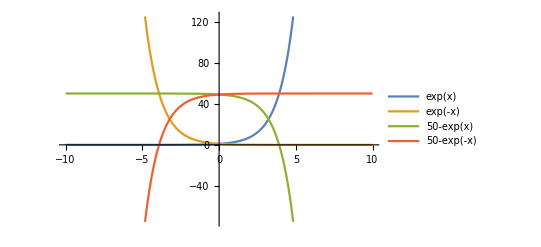

```mathematica
Plot[{Exp[x],Exp[-x],50-Exp[x],50-Exp[-x]},{x,-10,10},PlotLegends->"Expressions"]
```

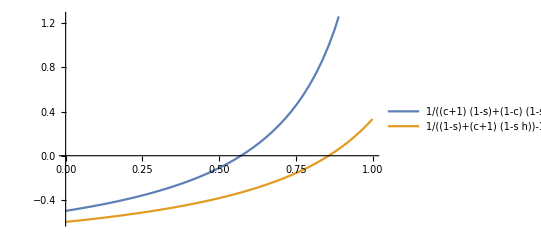

```mathematica
c = 0.5; h=0.5;
Plot[{(1/((c+1)*(1-s)+(1-c)*(1-s*h)))-1, (1/((1-s)+(c+1)*(1-s*h)))-1},{s,0,1},PlotLegends->"Expressions"]
```

```mathematica
Solve[(1/(2*(1-s)))-1 =0.1, s]
```

Set::write: Tag Plus in -1+1. is Protected.

Solve::ivar: 0.5 is not a valid variable.

Solve[0.1,0.5]